# Ejercicio : PushDown Automata

Estudiante : Andrey Arguedas Espinoza - 2020426569

## Código

Definimos la función POP

```mathematica
SetAttributes[Pop,HoldAll]
Pop[string_]:=Check[{StringTake[string,1],Check[string=StringDrop[string,1],string=""]},{"",""}]
```

Definimos la función PUSH

```mathematica
Push[string_,a_]:=StringInsert[string,a,1]
```

Hay que notar que el push retorna un string con el push aplicado, pero no modifica el original

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[
edges,
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight"
]
```

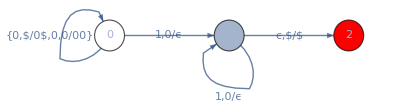

```mathematica
ShowGraphFA[{0->0,0->1,1 ->1,1->2},{0,1,2},{0},{2},{"{0,$/0$,0,0/00}","1,0/ϵ","1,0/ϵ","ϵ,$/$"}]
```

Definimos la asociación

```mathematica
δ= Association[
{0,"0","$"}->{0,"0$"},
{0,"0","0"}->{0,"00"},
{0,"1","0"}->{1,""},
{1,"1","0"}->{1,""},
{1,"","$"}->{2,"$"}
];

DeltaHat[{state_,string_,stack_}]:=Block[{trans, tempstack=stack,tempstring=string},
trans=δ[{state,First[Pop[tempstring]],First[Pop[tempstack]]}];
{First[trans],tempstring,Push[tempstack,Last[trans]]}
];
```

Debemos crear una función que nos de bajo la configuración que tenemos a cuales estados podemos llegar por medio de las transiciones EPSILON

```mathematica
Closure[currentState_, currentString_, currentStack_] := First[δ[{currentState,"",currentStack}]];
```

```mathematica
DeltaHatWithEpsilonClosure[{state_,string_,stack_}] := Block[{epsilonNextState,tempstack=stack,tempstring=string},
epsilonNextState=Closure[state,tempstring,StringTake[tempstack,1]];
{Check[DeltaHat[{state,string,stack}],Nothing],If[NumericQ[epsilonNextState],Check[DeltaHat[{epsilonNextState, tempstring, tempstack}],{epsilonNextState,tempstring,tempstack}], Nothing]}
];
```

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions[expression_,initialState_,stack_, times_]:=
Block[{},
root={initialState, expression,stack};
tree ={};
firstLevel =  DeltaHatWithEpsilonClosure[root];
NestList[Last[AppendTo[tree, Flatten[Table[DeltaHatWithEpsilonClosure[i],{i,#}],1]]]&,firstLevel,times-1];
{root,firstLevel /. {} -> Nothing, tree /. {} -> Nothing}
];
```

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions["01",0,"$",3]
```

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringInsert::string: String expected at position 2 in StringInsert[,{2,,$},1].

{{0,01,$},{{0,1,0$}},{{{1,,$}},{{2,,$}}}}

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions["0011",0,"$",5]
```

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringInsert::string: String expected at position 2 in StringInsert[,{2,,$},1].

{{0,0011,$},{{0,011,0$}},{{{0,11,00$}},{{1,1,0$}},{{1,,$}},{{2,,$}}}}

Veamos el ejemplo del palindrome

```mathematica
δ= Association[
{0,"0","$"}->{0,"0$"},
{0,"1","$"}->{0,"1$"},
{0,"0","0"}->{0,"00"},
{0,"0","1"}->{0,"01"},
{0,"1","0"}->{0,"10"},
{0,"1","1"}->{0,"11"},
{0,"","$"}->{1,"$"},
{0,"","0"}->{1,"0"},
{0,"","1"}->{1,"1"},
{1,"0","0"}->{1,""},
{1,"1","1"}->{1,""},
{1,"","$"}->{2,"$"},
{2,"","$"}->{2,"$"}
];
```

```mathematica
firstLevel = DeltaHatWithEpsilonClosure[{0,"1111","$"}]
```

StringInsert::string: String expected at position 2 in StringInsert[,{1,1,$},1].

{{0,111,1$},{1,1111,$}}

```mathematica
secondLevel = Flatten[Table[DeltaHatWithEpsilonClosure[i],{i,firstLevel}],1]
```

StringInsert::string: String expected at position 2 in StringInsert[,{1,1,$},1].

StringInsert::string: String expected at position 2 in StringInsert[,{2,1,$},1].

{{0,11,11$},{1,11,$},{2,1111,$}}

```mathematica
thirdLevel = Flatten[Table[DeltaHatWithEpsilonClosure[i],{i,secondLevel}],1]
```

StringInsert::string: String expected at position 2 in StringInsert[,{1,1,$},1].

StringInsert::string: String expected at position 2 in StringInsert[,{2,1,$},1].

General::stop: Further output of StringInsert::string will be suppressed during this calculation.

{{0,1,111$},{1,1,1$},{2,11,$},{2,1111,$}}

```mathematica
fourthLevel = Flatten[Table[DeltaHatWithEpsilonClosure[i],{i,thirdLevel}],1]
```

StringInsert::string: String expected at position 2 in StringInsert[,{2,1,$},1].

General::stop: Further output of StringInsert::string will be suppressed during this calculation.

{{0,,1111$},{1,,11$},{1,,$},{2,11,$},{2,1111,$}}

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions["1111", 0, "$", 4]
```

StringInsert::string: String expected at position 2 in StringInsert[,{1,1,$},1].

StringInsert::string: String expected at position 2 in StringInsert[,{2,1,$},1].

General::stop: Further output of StringInsert::string will be suppressed during this calculation.

{{0,1111,$},{{0,111,1$},{1,1111,$}},{{{0,11,11$},{1,11,$},{2,1111,$}},{{0,1,111$},{1,1,1$},{2,11,$},{2,1111,$}},{{0,,1111$},{1,,11$},{1,,$},{2,11,$},{2,1111,$}}}}